```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory_100um_2.72Best_withRF.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

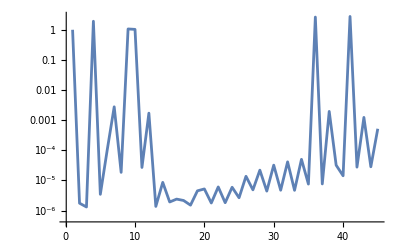

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-21.0136,L2PhaseSet→-38.0126,Q1EkG→150.814,Q2EkG→-167.965,Q3EkG→112.942,Q4EkG→126.585,Q5EkG→-23.5759,Q6EkG→-150.266,S1ELkG→1260.81,S2ELkG→-3911.03,S3ELkG→-4067.05,S3ERkG→-419.51,S2ERkG→-2966.63,S1ERkG→580.781,PDrive_mean_x→-0.0000843697,PDrive_mean_y→-7.85×10^-7,PDrive_sigma_x→0.0000283403,PDrive_sigma_y→0.000291578,PDrive_xCost→0.0000890024,PDrive_yCost→0.000291579,PDrive_totalCost→0.000190291,PDrive_emitSI90_x→0.0000494971,PDrive_emitSI90_y→0.000043807,PDrive_zLen→0.0000154857,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0000832971,PWitness_mean_y→2.324×10^-7,PWitness_sigma_x→0.0000217166,PWitness_sigma_y→0.000216591,PWitness_xCost→0.0000860815,PWitness_yCost→0.000216591,PWitness_totalCost→0.000151336,PWitness_emitSI90_x→0.000021912,PWitness_emitSI90_y→3.313×10^-6,PWitness_zLen→0.0000156309,PWitness_zCentroid→991.332,bunchSpacing→0.000106749,transverseCentroidOffset→1.4783×10^-6,maximizeMe→2.72491|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -21.0136370347
L2PhaseSet : -38.0126127044
Q1EkG : 150.8135181075
Q2EkG : -167.964977508
Q3EkG : 112.9423199037
Q4EkG : 126.5848609986
Q5EkG : -23.5758615542
Q6EkG : -150.2658118017
S1ELkG : 1260.8117634365
S2ELkG : -3911.0332889472
S3ELkG : -4067.0483875283
S3ERkG : -419.5097109132
S2ERkG : -2966.6280293031
S1ERkG : 580.7808051125
PDrive_mean_x : -0.0000843697
PDrive_mean_y : -7.85e-7
PDrive_sigma_x : 0.0000283403
PDrive_sigma_y : 0.0002915776
PDrive_xCost : 0.0000890024
PDrive_yCost : 0.0002915787
PDrive_totalCost : 0.0001902905
PDrive_emitSI90_x : 0.0000494971
PDrive_emitSI90_y : 0.000043807
PDrive_zLen : 0.0000154857
PDrive_zCentroid : 991.3317141432
PWitness_mean_x : -0.0000832971
PWitness_mean_y : 2.324e-7
PWitness_sigma_x : 0.0000217166
PWitness_sigma_y : 0.0002165907
PWitness_xCost : 0.0000860815
PWitness_yCost : 0.0002165909
PWitness_totalCost : 0.0001513362
PWitness_emitSI90_x : 0.000021912
PWitness_emitSI90_y : 3.313e-6
PWitness_zLen : 0.0000156309
PWitness_zCentroid : 991.3318208921
bunchSpacing : 0.0001067489
transverseCentroidOffset : 1.4783e-6
maximizeMe : 2.7249086834

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

1.47837×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv